# Cosmomathica v1.0

Santiago Casas, 2020

This notebook demonstrates how to use the Cosmomathica package version 1.0

## Calling external programs

### Initialization

First, load the Cosmomathica package

```mathematica
SetDirectory[NotebookDirectory[]]
```

/local/home/scasas/CosmoProjects/cosmomathica

```mathematica
ManToGif[man_,name_String,step_Integer]:=Export[name<>".gif",Import[Export[FileNameJoin[{NotebookDirectory[],"temp.avi"}],man],"ImageList"][[1;;-1;;step]]];
```

```mathematica
<<(NotebookDirectory[]<>"cosmomathica.m")
```

```mathematica
<<NumericalCalculus`
```

### CAMB

CAMB takes a lot of parameters. In Cosmomathica, most of them are being treated as options with default values while some of them are regular parameters that have to be specified. The distinction is arbitrary. These are the default options (see the CAMB documentation for details):

```mathematica
?CAMB
```

CAMB[OmegaC, OmegaB, h] :
provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes a few parameters as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.

```mathematica
Options[CAMB]
```

{MGflag→0,pureMGflag→1,altMGflag→1,QSAflag→1,mugammapar→2,musigmapar→1,QRpar→1,DEmodel→1,GRtrans→0.001,B1→0.,lambda12→0.,B2→0.,lambda22→0.,ss→4.,E11→0.,E22→0.,mu0→-1.,sigma0→0.,MGQfix→0.,MGRfix→0.,Qnot→1.,Rnot→1.,sss→0.,Lindergamma→0.545,betastar→0.,astar→0.5,xistar→0.001,beta0→1.,xi0→0.0001,DilS→0.24,DilR→1.,FR0→0.0001,FRn→1.,w0ppf→-1.,wappf→0.,Tcmb→2.7255,OmegaNu→0,OmegaK0→0.,YHe→0.24,MasslessNeutrinos→3.046,MassiveNeutrinos→0,NuMassDegeneracies→{0},NuMassFractions→{1},ScalarInitialCondition→adiabatic,NonLinear→pk,HalofitVersion→4,WantCMB→True,WantTransfer→True,WantCls→False,WantScalars→False,WantVectors→False,WantTensors→False,ScalarSpectralIndex→{0.96},ScalarRunning→{0},TensorSpectralIndex→{0},RatioScalarTensorAmplitudes→{1},ScalarPowerAmplitude→{2.1×10^-9},PivotScalar→0.05,PivotTensor→0.05,DoReionization→True,UseOpticalDepth→False,OpticalDepth→0.,ReionizationRedshift→10.,ReionizationFraction→1.,ReionizationDeltaRedshift→0.5,AccuracyBoost→2,TransferHighPrecision→True,TransferInterpMatterPower→False,WantZstar→True,WantZdrag→True,OutputNormalization→1,MaxEll→1500,MaxEtaK→4000.,MaxEtaKTensor→800.,MaxEllTensor→400,TransferKmax→5,TransferKperLogInt→50,TransferRedshifts→{0.},AccuratePolarization→True,AccurateReionization→False,AccurateBB→False,DoLensing→False,OnlyTransfers→False,DerivedParameters→True,MassiveNuMethod→best,debugIntFloats→False}

```mathematica
OptionValue[CAMB,#]&/@{ScalarSpectralIndex,ScalarPowerAmplitude,TransferKmax, HalofitVersion, NonLinear}
```

{{0.96},{2.1×10^-9},5,4,pk}

```mathematica
OptionValue[CAMB,#]&/@{MGflag,pureMGflag,altMGflag,QSAflag,mugammapar,musigmapar,DEmodel,GRtrans,FR0,FRn,w0ppf,wappf}
```

{0,1,1,1,2,1,1,0.001,0.0001,1.,-1.,0.}

```mathematica
OptionValue[CAMB,#]&/@{Tcmb, OmegaNu,MasslessNeutrinos,NuMassDegeneracies,NuMassFractions}
```

{2.7255,0,3.046,{0},{1}}

```mathematica
OptionValue[CAMB,#]&/@{AccuracyBoost,TransferHighPrecision,TransferInterpMatterPower}
```

{2,True,False}

```mathematica
?HalofitVersion
```

An option for CAMB. Integer number that chooses the Halofit version used in the non-linear matter power spectrum.
1: Original, 2: Bird, 3: Peacock, 4: Takahashi, 5: Mead, 6: Halo model, 7: Casarini,
8: Mead2015, 9: Winther-f(R)

```mathematica
redsub=Subdivide[0.,50.,99];
```

```mathematica
redshifts=Reverse[redsub(*Range[0,50,0.1]*)(*Join~{20,100}*)];
```

```mathematica
redzrang=Range[Length[redshifts]];
```

```mathematica
ClearAll[cambdata]
```

```mathematica
computeOmegaCNuParams[OmegaM_, OmegaB_, hubble_, MnuTotal_]:=Block[{Neff = 3.046, omgref,OmegaRDS, masslessnus, 
numassfac=94.07(*eV*), massivenus, omeganuh2,
OmegaNu, OmegaC},
Which[
MnuTotal==0.06,
massivenus=1; 
,
MnuTotal==0.15,
massivenus=3; 
,
MnuTotal==0.,
massivenus=0; 
];
omgref = (2.469/hubble^2)*10^(-5);
OmegaRDS = omgref*(1. + 0.2271*Neff);
masslessnus=Neff-massivenus;
omeganuh2=Sum[(((Neff/3)^(3/4))*(MnuTotal/massivenus))/numassfac, {i,1,massivenus}];
OmegaNu=omeganuh2/(hubble^2);
OmegaC=OmegaM-OmegaB-OmegaNu;
Return[{OmegaC, OmegaNu, massivenus, masslessnus}]
]
```

```mathematica
(*Standard LCDM, massless neutrinos*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]

cambdata[0]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->4,
MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1} ];

(CAMB["sigma8(z)"]/.cambdata[0])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.27

OmegaB= 0.05

OmegaNu= 0.

0.824894

```mathematica
cambdata[0][[All,1]]
```

{CAMB[age],CAMB[zstar],CAMB[rstar],CAMB[100thetastar],CAMB[zdrag],CAMB[rdrag],CAMB[kD],CAMB[100thetaD],CAMB[zEQ],CAMB[100thetaEQ],CAMB[H(z)],CAMB[sigma8(z)],CAMB[f(z)],CAMB[D+(z)],CAMB[CLscalar],CAMB[redshifts],CAMB[PSlinear],CAMB[PSnonlinear],CAMB[Transfer]}

```mathematica
(*Standard LCDM, massive neutrinos, MntTotal=0.06eV*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.06; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[1]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->4,
MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1} ];

(CAMB["sigma8(z)"]/.cambdata[1])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.268563

OmegaB= 0.05

OmegaNu= 0.00143717

Massless Nus = 2.046

0.810564

```mathematica
?DEmodel
```

An option for CAMB/MGCAMB:
DE_model = 0 : LCDM
DE_model = 1 : wCDM        
DE_model = 2 : (w0,wa)CDM  
DE_model = 3 : user defined

```mathematica
(* w0waCDM , non-Lambda, massless neutrinos, MNuTotal=0eV, HalofitVersion=Mead (=5)*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-0.9; weqa=0.05;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.0; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[2]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->5,
MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1}, w0ppf->weq0, wappf->weqa,DEmodel->1];

(CAMB["sigma8(z)"]/.cambdata[2])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.27

OmegaB= 0.05

OmegaNu= 0.

Massless Nus = 3.046

0.802718

```mathematica
(*f(R) theory, massless neutrinos, fR0=10^-4*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[34]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True,
 HalofitVersion->9, MGflag->3, QSAflag->4, FR0->10^(-4), FRn->1, DEmodel->0, MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1}];

(CAMB["sigma8(z)"]/.cambdata[34])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.27

OmegaB= 0.05

OmegaNu= 0.

Massless Nus = 3.046

0.941074

```mathematica
(*f(R) theory, massless neutrinos, fR0=10^-4*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[35]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True,
 HalofitVersion->9, MGflag->3, QSAflag->4, FR0->10^(-5), FRn->1, DEmodel->0, MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1}];

(CAMB["sigma8(z)"]/.cambdata[35])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.27

OmegaB= 0.05

OmegaNu= 0.

Massless Nus = 3.046

0.877885

```mathematica
(*f(R) theory, massless neutrinos, fR0=10^-4*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.06; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[351]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True,
 HalofitVersion->9, MGflag->3, QSAflag->4, FR0->10^(-5), FRn->1, DEmodel->0, MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1}];

(CAMB["sigma8(z)"]/.cambdata[351])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.268563

OmegaB= 0.05

OmegaNu= 0.00143717

Massless Nus = 2.046

0.862701

```mathematica
(*f(R) theory, massless neutrinos, fR0=10^-4*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[36]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True,
 HalofitVersion->9, MGflag->3, QSAflag->4, FR0->10^(-6), FRn->1, DEmodel->0, MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1}];

(CAMB["sigma8(z)"]/.cambdata[36])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.27

OmegaB= 0.05

OmegaNu= 0.

Massless Nus = 3.046

0.837861

```mathematica
(* ModifiedGravity, muGamma Parametrization, LCDM background,  HalofitVersion->4, MGflag->1, pureMGflag->1,
 DEmodel->0, GRtrans->0.001, E11->0.1007, E22->0.8293, mugammapar ->2, massless neutrinos, HalofitVersion=4 Takahashi*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.0; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[4]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->5,
MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1},  HalofitVersion->4, MGflag->1, pureMGflag->1,
 DEmodel->0, GRtrans->0.001, E11->0.1007, E22->0.8293, mugammapar ->2 ];

(CAMB["sigma8(z)"]/.cambdata[4])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.27

OmegaB= 0.05

OmegaNu= 0.

Massless Nus = 3.046

0.831933

```mathematica
(* ModifiedGravity, muGamma Parametrization, LCDM background,  HalofitVersion->4, MGflag->1, pureMGflag->1,
 DEmodel->0, GRtrans->0.001, E11->0.1007, E22->0.8293, mugammapar ->2, massless neutrinos, HalofitVersion=4 Takahashi*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.06; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[4]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->5,
MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1},  HalofitVersion->4, MGflag->1, pureMGflag->1,
 DEmodel->0, GRtrans->0.001, E11->0.1007, E22->0.8293, mugammapar ->2 ];

(CAMB["sigma8(z)"]/.cambdata[4])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.268563

OmegaB= 0.05

OmegaNu= 0.00143717

Massless Nus = 2.046

0.817185

```mathematica
(*Do[
Print["ii:", ii];
cambdata[ii]=CAMB[0.25,0.05,0.67,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->9, MGflag->3, QSAflag->4, FR0->10^(-ii), FRn->1, DEmodel->0];
,{ii,{4,5,6}}]*)
```

```mathematica
redshifts=CAMB["redshifts"]/.cambdata[0]
```

{50.,49.4949,48.9899,48.4848,47.9798,47.4747,46.9697,46.4646,45.9596,45.4545,44.9495,44.4444,43.9394,43.4343,42.9293,42.4242,41.9192,41.4141,40.9091,40.404,39.899,39.3939,38.8889,38.3838,37.8788,37.3737,36.8687,36.3636,35.8586,35.3535,34.8485,34.3434,33.8384,33.3333,32.8283,32.3232,31.8182,31.3131,30.8081,30.303,29.798,29.2929,28.7879,28.2828,27.7778,27.2727,26.7677,26.2626,25.7576,25.2525,24.7475,24.2424,23.7374,23.2323,22.7273,22.2222,21.7172,21.2121,20.7071,20.202,19.697,19.1919,18.6869,18.1818,17.6768,17.1717,16.6667,16.1616,15.6566,15.1515,14.6465,14.1414,13.6364,13.1313,12.6263,12.1212,11.6162,11.1111,10.6061,10.101,9.59596,9.09091,8.58586,8.08081,7.57576,7.07071,6.56566,6.06061,5.55556,5.05051,4.54545,4.0404,3.53535,3.0303,2.52525,2.0202,1.51515,1.0101,0.505051,0.}

```mathematica
redshifts//Dimensions
```

{100}

```mathematica
redshifts
```

{50.,49.4949,48.9899,48.4848,47.9798,47.4747,46.9697,46.4646,45.9596,45.4545,44.9495,44.4444,43.9394,43.4343,42.9293,42.4242,41.9192,41.4141,40.9091,40.404,39.899,39.3939,38.8889,38.3838,37.8788,37.3737,36.8687,36.3636,35.8586,35.3535,34.8485,34.3434,33.8384,33.3333,32.8283,32.3232,31.8182,31.3131,30.8081,30.303,29.798,29.2929,28.7879,28.2828,27.7778,27.2727,26.7677,26.2626,25.7576,25.2525,24.7475,24.2424,23.7374,23.2323,22.7273,22.2222,21.7172,21.2121,20.7071,20.202,19.697,19.1919,18.6869,18.1818,17.6768,17.1717,16.6667,16.1616,15.6566,15.1515,14.6465,14.1414,13.6364,13.1313,12.6263,12.1212,11.6162,11.1111,10.6061,10.101,9.59596,9.09091,8.58586,8.08081,7.57576,7.07071,6.56566,6.06061,5.55556,5.05051,4.54545,4.0404,3.53535,3.0303,2.52525,2.0202,1.51515,1.0101,0.505051,0.}

```mathematica
transfer=CAMB["Transfer"]/.cambdata[0];
```

```mathematica
transfer//Dimensions
```

{100,363,14}

```mathematica
(* redshifts length, k-values length and 14 transfer quantities*)
```

```mathematica
kvalues = transfer[[1,All,1]];
```

```mathematica
kvalues//Dimensions
```

{363}

```mathematica
pkLinear=CAMB["PSlinear"]/.cambdata[0];
```

```mathematica
pkLinear//Dimensions
```

{100,363,2}

```mathematica
kvaluesFromPk = pkLinear[[1]][[All,1]];
```

```mathematica
kvaluesFromPk//Dimensions
```

{363}

```mathematica
Total[Chop[kvalues-kvaluesFromPk, 10^-10]]
```

0

```mathematica
Interrupt[]
```

$Aborted

```mathematica
pkLinear[[100,363]][[2]]
```

1.3136

## Compute Interpolated Quantities and Arrays

```mathematica
totalmodlist={0,1,2,4, 34, 35, 351, 36}
```

{0,1,2,4,34,35,351,36}

```mathematica
modelsname={"LCDM","LCDM_Mν","w0waCDM","MG_μ-η", "f(R)-4", "f(R)-5","f(R)-5_Mν",  "f(R)-6"}
```

{LCDM,LCDM_Mν,w0waCDM,MG_μ-η,f(R)-4,f(R)-5,f(R)-5_Mν,f(R)-6}

```mathematica
ClearAll[kvals,psl, psnl, growthCAMB, fgrowthrateCAMB,growthRatioPksLin,growthRatioPksNonLin, s8growth, s8fgrowthrate, Hofz, redshiftsz]
```

```mathematica
Do[
redshiftsz[ii_]:=(CAMB["redshifts"]/.cambdata[ii]);
scalefactor[ii_][zind_]:=(1/redshiftsz[0][[zind]]);
kvals[ii_]:=((CAMB["PSlinear"]/.cambdata[ii])[[1,All,1]]);
psl[ii_][zind_,kind_]:=((CAMB["PSlinear"]/.cambdata[ii])[[zind,kind,2]]);
psnl[ii_][zind_,kind_]:=((CAMB["PSnonlinear"]/.cambdata[ii])[[zind,kind,2]]);
growthCAMB[ii_][zind_,kind_]:=(((CAMB["Transfer"]/.cambdata[ii])[[zind, kind,7]])/((CAMB["Transfer"]/.cambdata[ii])[[-1, kind,7]]));
fgrowthrateCAMB[ii_][zind_,kind_]:=((CAMB["Transfer"]/.cambdata[ii])[[zind, kind,14]])/((CAMB["Transfer"]/.cambdata[ii])[[1, kind,14]]);
s8growth[ii_][zind_]:=((CAMB["D+(z)"]/.cambdata[ii])[[zind]]);
s8fgrowthrate[ii_][zind_]:=((CAMB["f(z)"]/.cambdata[ii])[[zind]]);
growthRatioPksLin[ii_][zind_,kind_]:=Sqrt[psl[ii][zind,kind]/psl[ii][-1,kind]];
growthRatioPksNonLin[ii_][zind_,kind_]:=Sqrt[psnl[ii][zind,kind]/psnl[ii][-1,kind]];
Hofz[ii_][zind_]:=((CAMB["H(z)"]/.cambdata[ii])[[zind]]);
,
{ii,totalmodlist}]

(*Export["./powerspectra/cosmomathica-fR-"<>ToString[ii]<>"-pk_lin-z_"<>ToString[Length[redshifts]-redz]<>".txt", Transpose[{kvals[ii][redz],psl[ii][redz]}], "Table"];*)
(*Export["./powerspectra/cosmomathica-fR-"<>ToString[ii]<>"-pk_nonlin-z_"<>ToString[Length[redshifts]-redz]<>".txt", Transpose[{kvals[ii][redz],psnl[ii][redz]}], "Table"];*)
```

```mathematica
kvals[0];
```

```mathematica
redshiftsz[0]
```

{50.,49.4949,48.9899,48.4848,47.9798,47.4747,46.9697,46.4646,45.9596,45.4545,44.9495,44.4444,43.9394,43.4343,42.9293,42.4242,41.9192,41.4141,40.9091,40.404,39.899,39.3939,38.8889,38.3838,37.8788,37.3737,36.8687,36.3636,35.8586,35.3535,34.8485,34.3434,33.8384,33.3333,32.8283,32.3232,31.8182,31.3131,30.8081,30.303,29.798,29.2929,28.7879,28.2828,27.7778,27.2727,26.7677,26.2626,25.7576,25.2525,24.7475,24.2424,23.7374,23.2323,22.7273,22.2222,21.7172,21.2121,20.7071,20.202,19.697,19.1919,18.6869,18.1818,17.6768,17.1717,16.6667,16.1616,15.6566,15.1515,14.6465,14.1414,13.6364,13.1313,12.6263,12.1212,11.6162,11.1111,10.6061,10.101,9.59596,9.09091,8.58586,8.08081,7.57576,7.07071,6.56566,6.06061,5.55556,5.05051,4.54545,4.0404,3.53535,3.0303,2.52525,2.0202,1.51515,1.0101,0.505051,0.}

```mathematica
{kvals,psl, psnl, growthCAMB, fgrowthrateCAMB,growthRatioPksLin,growthRatioPksNonLin, s8growth, s8fgrowthrate, Hofz, redshiftsz}
```

{kvals,psl,psnl,growthCAMB,fgrowthrateCAMB,growthRatioPksLin,growthRatioPksNonLin,s8growth,s8fgrowthrate,Hofz,redshiftsz}

```mathematica
(*reshap=ArrayReshape[growthTab[0][[All,2]], {Length@revZrang[0], Length@krang[0]}];
reshap//Dimensions*)
```

```mathematica
ClearAll[revZrang];  ClearAll["*Interp"]; ClearAll["*Tab"]; ClearAll[krang];
```

ClearAll::wrsym: Symbol Tab is Protected.

```mathematica
krang[mod_]:=krang[mod]=Range[Length[kvals[mod]]];
revZrang[mod_]:=revZrang[mod]=Reverse[Range[Length[redshiftsz[mod]]]];
growthCAMBTab[mod_]:=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},growthCAMB[mod][zzi,kki]},{zzi,revZrang[mod]},{kki,krang[mod] }],1];
growthCAMBInterp[mod_]:=growthCAMBInterp[mod]=Interpolation[growthCAMBTab[mod], InterpolationOrder->3, Method->"Spline"];
fgrowthrateCAMBTab[mod_]:=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},fgrowthrateCAMB[mod][zzi,kki]},{zzi,revZrang[mod]},{kki,krang[mod] }],1];
fgrowthrateCAMBInterp[mod_]:=fgrowthrateCAMBInterp[mod]=Interpolation[fgrowthrateCAMBTab[mod], InterpolationOrder->3, Method->"Spline"];
pkLinTab[mod_]:=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},psl[mod][zzi,kki]},{zzi,Range[Length[redshiftsz[mod]]]},{kki, Range[Length[kvals[mod]]]}],1];
pkNonLinTab[mod_]:=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},psnl[mod][zzi,kki]},{zzi,Range[Length[redshiftsz[mod]]]},{kki, Range[Length[kvals[mod]]]}],1];
pkLinInterp[mod_]:=pkLinInterp[mod]=Interpolation[pkLinTab[mod], InterpolationOrder->1, Method->"Spline"];
pkNonLinInterp[mod_]:=pkNonLinInterp[mod]=Interpolation[pkNonLinTab[mod], InterpolationOrder->1, Method->"Spline"];

s8growthInterp[mod_]:=s8growthInterp[mod]=Interpolation[Table[{redshiftsz[mod][[zzi]],s8growth[mod][zzi]}, {zzi,1,Length[redshiftsz[mod]]}], InterpolationOrder->3, Method->"Spline"];
s8fgrowthrateInterp[mod_]:=s8fgrowthrateInterp[mod]=Interpolation[Table[{redshiftsz[mod][[zzi]],s8fgrowthrate[mod][zzi]}, {zzi,1,Length[redshiftsz[mod]]}], InterpolationOrder->3, Method->"Spline"];


growthRatioPksLinTab[mod_]:=growthRatioPksLinTab[mod]=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},growthRatioPksLin[mod][zzi,kki]},{zzi,revZrang[mod]},{kki,krang[mod] }],1];
growthRatioPksLinTabInterp[mod_]:=growthRatioPksLinTabInterp[mod]=Interpolation[growthRatioPksLinTab[mod], InterpolationOrder->3, Method->"Spline"];

growthRatioPksNonLinTab[mod_]:=growthRatioPksNonLinTab[mod]=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},growthRatioPksNonLin[mod][zzi,kki]},{zzi,revZrang[mod]},{kki,krang[mod] }],1];
growthRatioPksNonLinTabInterp[mod_]:=growthRatioPksNonLinTabInterp[mod]=Interpolation[growthRatioPksNonLinTab[mod], InterpolationOrder->3, Method->"Spline"];

fgRatioPksLinInterp[mod_][z_, ka_]:=Block[{zz},-(1+z)*ND[Log[growthRatioPksLinTabInterp[mod][zz,ka]],zz,z]];
fgRatioPksNonLinInterp[mod_][z_, ka_]:=Block[{zz},-(1+z)*ND[Log[growthRatioPksNonLinTabInterp[mod][zz,ka]],zz,z]];
```

```mathematica
Interrupt[]
```

$Aborted

## Plot Functions

```mathematica
colorarra=ColorData["DarkRainbow"][#]&/@Subdivide[1,6]
```

{RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.2608336666666667, 0.3969803333333333, 0.4426503333333333],RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335],RGBColor[0.624866, 0.673302, 0.264296],RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333],RGBColor[0.7851613333333333, 0.4255956666666667, 0.279293],RGBColor[0.72987, 0.239399, 0.230961]}

```mathematica
totalmodlist
```

{0,1,2,4,34,35,351,36}

```mathematica
modelsnamerule=Thread[Rule[totalmodlist,modelsname]]
```

{0→LCDM,1→LCDM_Mν,2→w0waCDM,4→MG_μ-η,34→f(R)-4,35→f(R)-5,351→f(R)-5_Mν,36→f(R)-6}

```mathematica
{0,1,4}/.modelsnamerule
```

{LCDM,LCDM_Mν,MG_μ-η}

```mathematica
Length@colorarra
```

7

```mathematica
overallStyles=Thread[{ConstantArray[Thick,Length@colorarra],Thread[{colorarra,Table[AbsoluteDashing[{r,6-r}],{r,{1,2,3,4,5,6,7}}]}]}]
```

{{Thickness[Large],{RGBColor[0.237736, 0.340215, 0.575113],AbsoluteDashing[{1,5}]}},{Thickness[Large],{RGBColor[0.2608336666666667, 0.3969803333333333, 0.4426503333333333],AbsoluteDashing[{2,4}]}},{Thickness[Large],{RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335],AbsoluteDashing[{3,3}]}},{Thickness[Large],{RGBColor[0.624866, 0.673302, 0.264296],AbsoluteDashing[{4,2}]}},{Thickness[Large],{RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333],AbsoluteDashing[{5,1}]}},{Thickness[Large],{RGBColor[0.7851613333333333, 0.4255956666666667, 0.279293],AbsoluteDashing[{6,0}]}},{Thickness[Large],{RGBColor[0.72987, 0.239399, 0.230961],AbsoluteDashing[{7,-1}]}}}

```mathematica
ClearAll[raplonl];
```

```mathematica
raplonl[modlist_,zz_,lin_?BooleanQ, plrang_:Full]:=Block[{pk},
If[lin,pk=pkLinInterp,pk=pkNonLinInterp];
LogLogPlot[Evaluate@(((pk[#][zz,kkk]/pk[0][zz,kkk])&/@modlist)) ,
{kkk,0.0001,5}, Frame->True, FrameLabel->{"", Style["P_model(k)/P_LCDM(k)", Bold, 10]} , 
ImageSize->{300,150}, FrameTicksStyle->Directive[Black,10],
PlotStyle->overallStyles, PlotRange->plrang]];
```

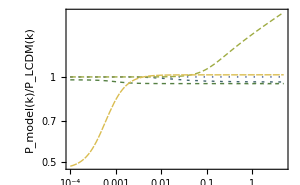

```mathematica
raplonl[{0,1,2,3,4},0.,True]
```

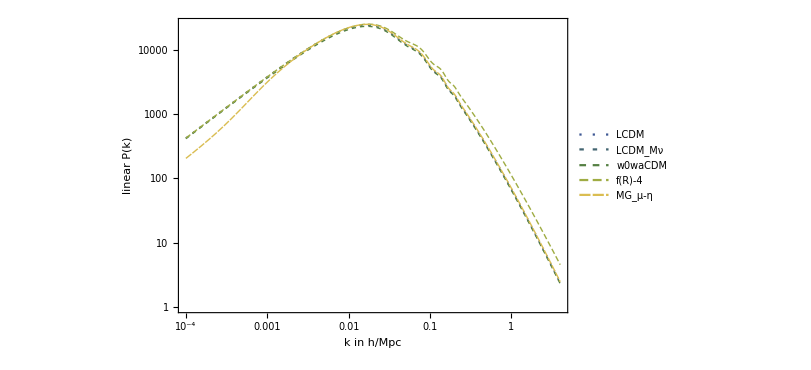

```mathematica
ClearAll[pk];
linBool=True;
plotmodlist={0,1,2,34,4};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLogPlot[Evaluate@((pk[#][zplot,kkk]&/@plotmodlist)), {kkk,0.0001,4},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["linear P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]]
```

```mathematica
modelsnamerule
```

{0→LCDM,1→LCDM_Mν,2→w0waCDM,4→MG_μ-η,34→f(R)-4,35→f(R)-5,36→f(R)-6}

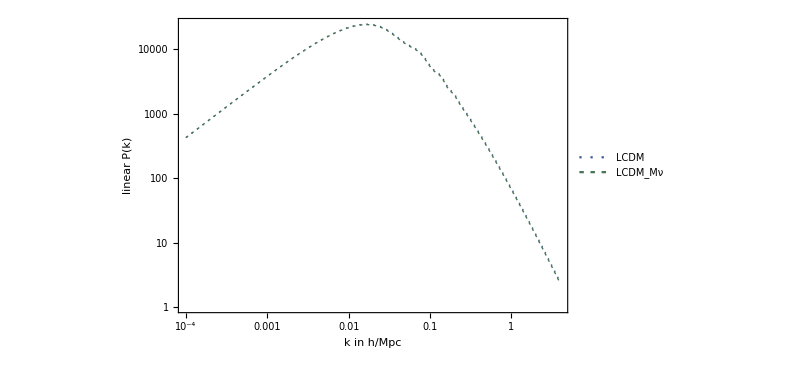

```mathematica
ClearAll[pk];
linBool=True;
plotmodlist={0,1};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLogPlot[Evaluate@((pk[#][zplot,kkk]&/@plotmodlist)), {kkk,0.0001,4},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.85,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["linear P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplonl[plotmodlist,zplot,linBool, {0.9,1.1}], Scaled[{0.5,0.3}]]]
```

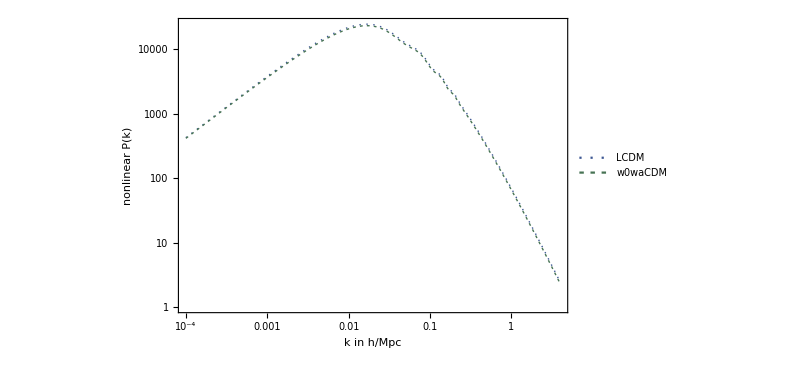

```mathematica
ClearAll[pk];
linBool=True;
plotmodlist={0,2};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLogPlot[Evaluate@((pk[#][zplot,kkk]&/@plotmodlist)), {kkk,0.0001,4},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.1,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["nonlinear P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplonl[plotmodlist,zplot,linBool, {0.9,1.1}], Scaled[{0.5,0.3}]]]
```

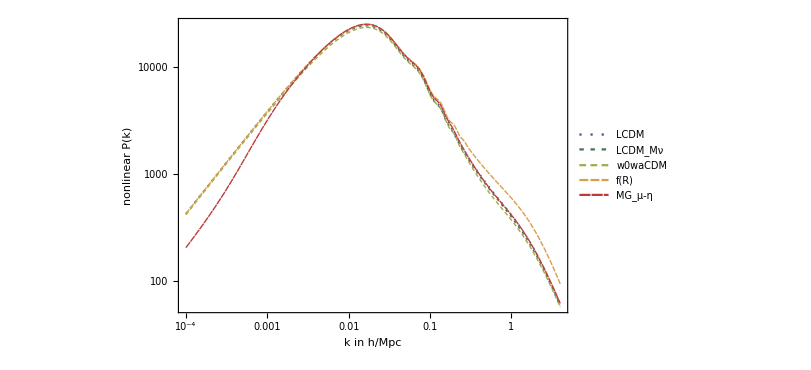

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1,2,3,4};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLogPlot[Evaluate@((pk[#][zplot,kkk]&/@plotmodlist)), {kkk,0.0001,4},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["nonlinear P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]]
```

```mathematica
overallPlotRange={0.2,1.1};
```

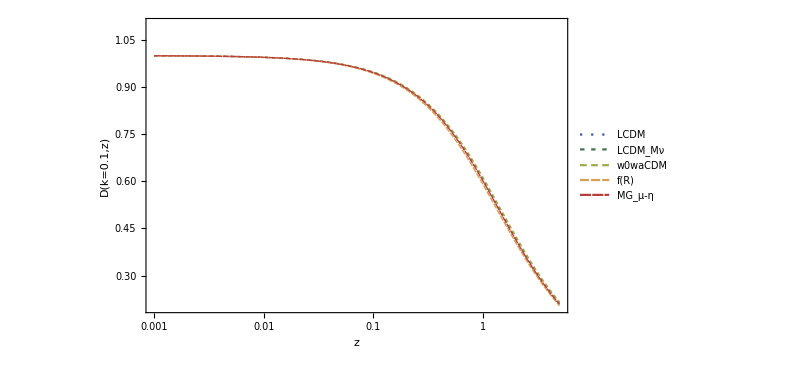

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1,2,3,4};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((growthCAMBInterp[#][zz, 0.1]&/@plotmodlist)), {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style["D(k=0.1,z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->overallPlotRange(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

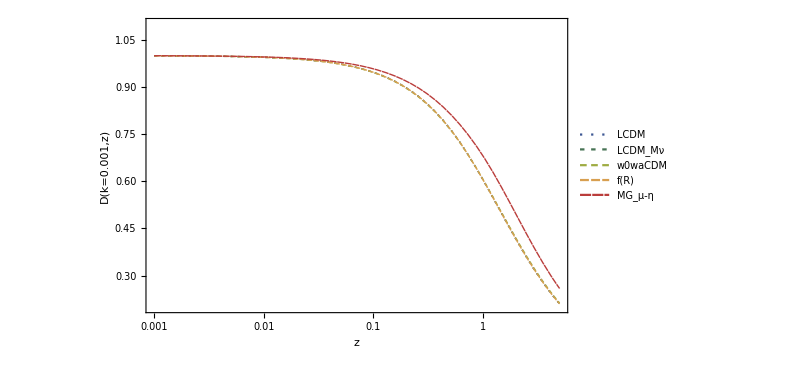

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1,2,3,4};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((growthCAMBInterp[#][zz, 0.0005]&/@plotmodlist)), {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style["D(k=0.001,z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->overallPlotRange(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

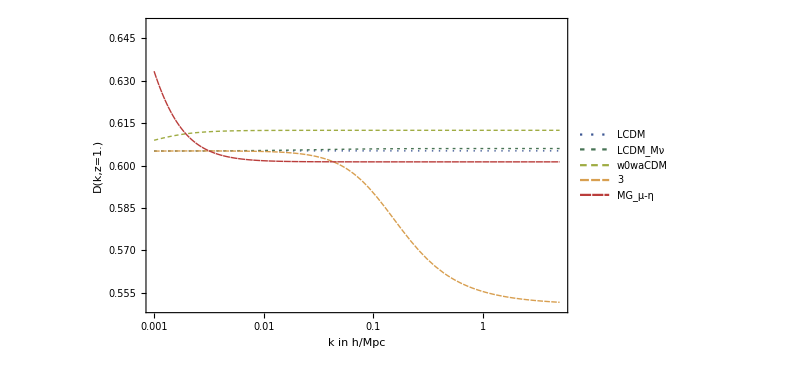

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1,2,3,4};
zplot=1.0;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((growthCAMBInterp[#][zplot, kkk]&/@plotmodlist)), {kkk,0.001,5},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["D(k,z="<>ToString[zplot]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16](*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*), PlotRange->{0.55,0.65}]
```

```mathematica
modelsnamerule
```

{0→LCDM,1→LCDM_Mν,2→w0waCDM,4→MG_μ-η,34→f(R)-4,35→f(R)-5,36→f(R)-6}

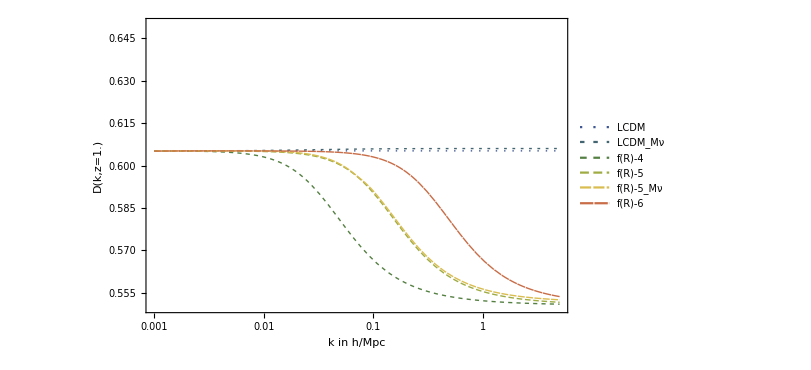

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1,34, 35,351, 36};
zplot=1.0;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((growthCAMBInterp[#][zplot, kkk]&/@plotmodlist)), {kkk,0.001,5},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["D(k,z="<>ToString[zplot]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16](*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*), PlotRange->{0.55,0.65}]
```

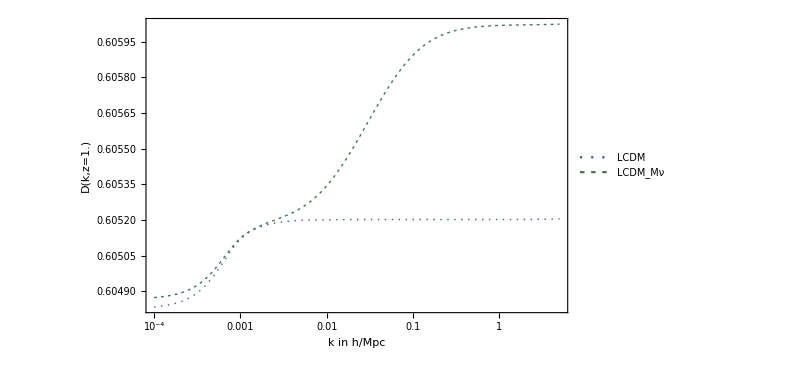

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1};
zplot=1.0;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((growthCAMBInterp[#][zplot, kkk]&/@plotmodlist)), {kkk,0.0001,5},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["D(k,z="<>ToString[zplot]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16](*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*), PlotRange->Full]
```

```mathematica
modelsnamerule
```

{0→LCDM,1→LCDM_Mν,2→w0waCDM,3→f(R),4→MG_μ-η}

```mathematica
manDkzFR=Manipulate[LogLogPlot[{growthCAMBInterp[0][zvalue,kkk],growthCAMBInterp[2][zvalue,kkk],growthCAMBInterp[4][zvalue,kkk]}, {kkk,0.0001,4.0}, PlotLegends->{"LCDM", "fR0=10^-4", "MGmugamma"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["k", Bold,16],Style[ "D(z,k)", Bold, 16]}, Epilog->Inset[Style["z="<>ToString[zvalue], Bold, 14],Scaled[{0.2,0.2}]], 
PlotRange->{0.4,1.05}      ],{zvalue, 0.001,10, 0.01}]
```

```mathematica
modelsnamerule
```

{0→LCDM,1→LCDM_Mν,2→w0waCDM,3→f(R),4→MG_μ-η}

```mathematica
manfgkzFR=Manipulate[LogLogPlot[{fgrowthrateCAMBInterp[0][zvalue,kkk],fgrowthrateCAMBInterp[2][zvalue,kkk],fgrowthrateCAMBInterp[4][zvalue,kkk]}, {kkk,0.0001,4.0}, PlotLegends->{"LCDM", "fR0=10^-4", "MGmugamma"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["k", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["z="<>ToString[zvalue], Bold, 14],Scaled[{0.2,0.2}]], 
PlotRange->{0.4,1.05}      ],{zvalue, 0.001,10, 0.01}]
```

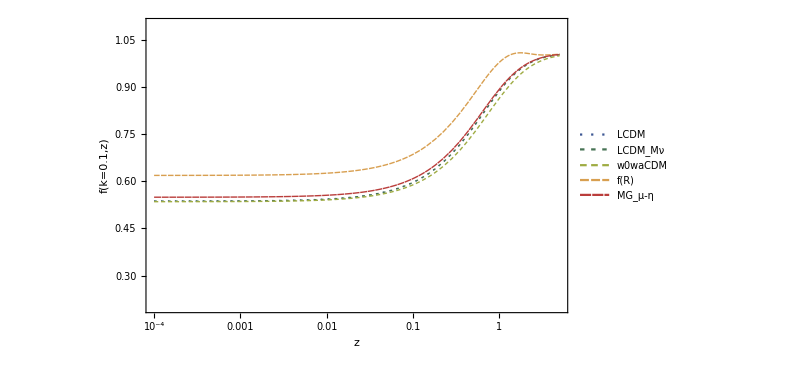

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1,2,3,4};
zplot=0.;
kplot=0.1;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((fgrowthrateCAMBInterp[#][zz, kplot]&/@plotmodlist)), {zz,0.0001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style["f(k="<>ToString[kplot]<>",z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->overallPlotRange(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

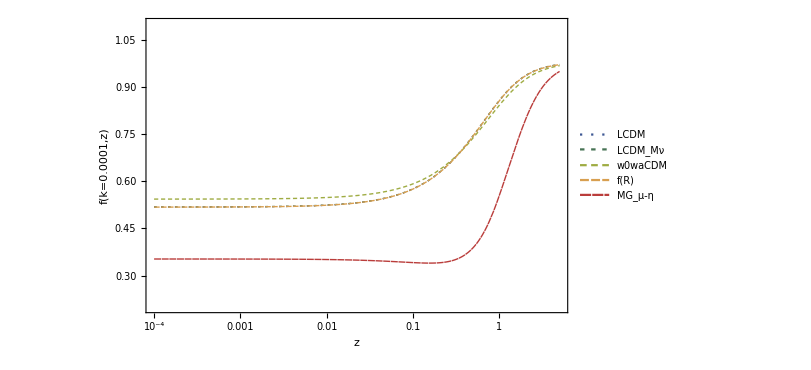

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1,2,3,4};
zplot=0.;
kplot=0.0001;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((fgrowthrateCAMBInterp[#][zz, kplot]&/@plotmodlist)), {zz,0.0001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style["f(k="<>ToString[kplot]<>",z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->overallPlotRange(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

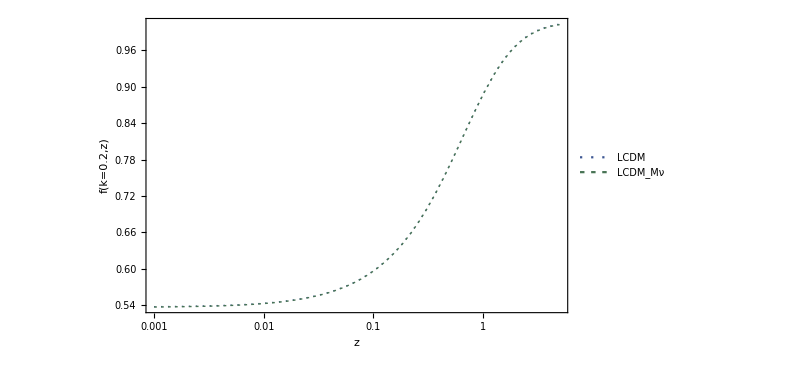

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1};
zplot=0.;
kplot=0.2;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((fgrowthrateCAMBInterp[#][zz, kplot]&/@plotmodlist)), {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style["f(k="<>ToString[kplot]<>",z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->Full(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

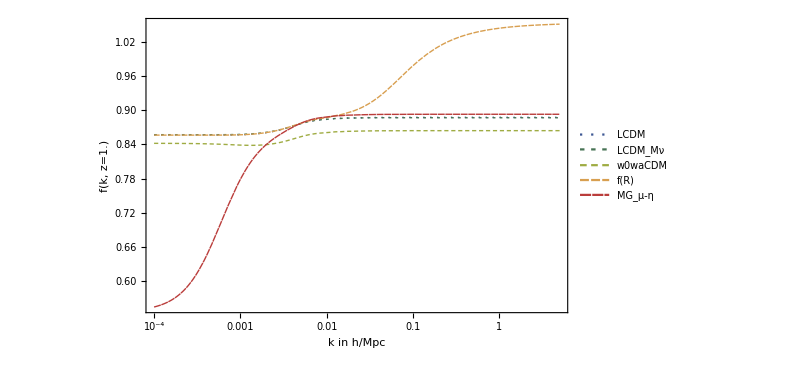

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1,2,3,4};
zplot=1.0;
kplot=0.0001;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((fgrowthrateCAMBInterp[#][zplot, kk]&/@plotmodlist)), {kk,0.0001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["f(k, z="<>ToString[zplot]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->Full(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

## Plot different options for Growth

```mathematica
(*ManToGif[manDkzFR,FileNameJoin[{NotebookDirectory[],"Dkz-fR"}],1]*)
```

```mathematica
(*manFzkFR=Manipulate[LogPlot[{fgInterp[0][zzz,kpoint],fgInterp[4][zzz,kpoint],fgInterp[6][zzz,kpoint]}, {zzz,0.,10.0}, PlotLegends->{"LCDM", "fR0=10^-4", "fR0=10^-6"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->{0.8,1.2}  ], {kpoint, 10^-4,2,0.001}]*)
```

```mathematica
(*Manipulate[LogPlot[{growthrateCAMBInterp[4][zzz,kpoint],fgInterp[4][zzz,kpoint]}, {zzz,0.,10.0}, PlotLegends->{"f4-camb", "f4-deriv"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->All  ], {kpoint, 10^-4,2,0.001}]*)
```

```mathematica
(*Manipulate[LogPlot[{growthrateCAMBInterp[6][zzz,kpoint]/fgInterp[6][zzz,kpoint]}, {zzz,0.,10.0}, PlotLegends->{"f4-camb", "f4-deriv"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->All  ], {kpoint, 10^-4,2,0.001}]*)
```

```mathematica
(*ManToGif[manFzkFR,FileNameJoin[{NotebookDirectory[],"fG_zk-fR"}],1]*)
```

```mathematica
(*Manipulate[LogLinearPlot[{fgInterp[0][zpoint,kkk],fgInterp[4][zpoint,kkk],fgInterp[6][zpoint,kkk]}, {kkk,0.0001,4.0}, PlotLegends->{"LCDM", "fR0=10^-4", "fR0=10^-6"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["k", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["z="<>ToString[N@zpoint], Bold, 14],Scaled[{0.8,0.2}]]    (*PlotRange->{0.8,1.2}*)  ], {zpoint, 0.,9.9}]*)
```

```mathematica
(*Manipulate[LogPlot[{fgInterp[0][zzz,kpoint],fgInterp[4][zzz,kpoint],fgInterp[6][zzz,kpoint], s8growthrateInterp[4][zzz]}, {zzz,0.,10.0}, PlotLegends->{"LCDM", "logfR0=-4", "logfR0=-6", "k=s8_logfR0=-4"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->{0.8,1.2}  ], {kpoint, 10^-4,2,0.001}]*)
```

```mathematica
(*Manipulate[LogLinearPlot[{fgInterp[0][zpoint,kkk],fgInterp[4][zpoint,kkk],fgInterp[6][zpoint,kkk], s8growthrateInterp[4][zpoint]}, {kkk,0.0001,4.0}, PlotLegends->{"LCDM", "fR0=10^-4", "fR0=10^-6", "k=s8_logfR0=-4"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["k", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["z="<>ToString[N@zpoint], Bold, 14],Scaled[{0.8,0.2}]]    (*PlotRange->{0.8,1.2}*)  ], {zpoint, 0.,9.9}]*)
```

```mathematica
Names["*Interp"]
```

{fgRatioPksLinInterp,fgRatioPksNonLinInterp,fgrowthrateCAMBInterp,growthCAMBInterp,growthRatioPksLinTabInterp,growthRatioPksNonLinTabInterp,pkLinInterp,pkNonLinInterp,s8fgrowthrateInterp,s8growthInterp}

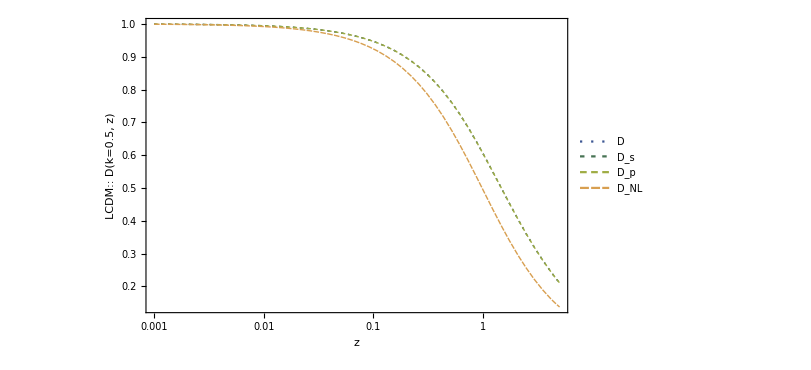

```mathematica
modelnum=0;
modelname=modelnum/.modelsnamerule;
kvall=0.5;
LogLinearPlot[{growthCAMBInterp[modelnum][zz, kvall],s8growthInterp[modelnum][zz],growthRatioPksLinTabInterp[modelnum][zz,kvall], growthRatioPksNonLinTabInterp[modelnum][zz,kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"D","D_s","D_p", "D_NL"}], Scaled[{0.15,0.3}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style[modelname<>":: "<>"D(k="<>ToString[kvall]<>", z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

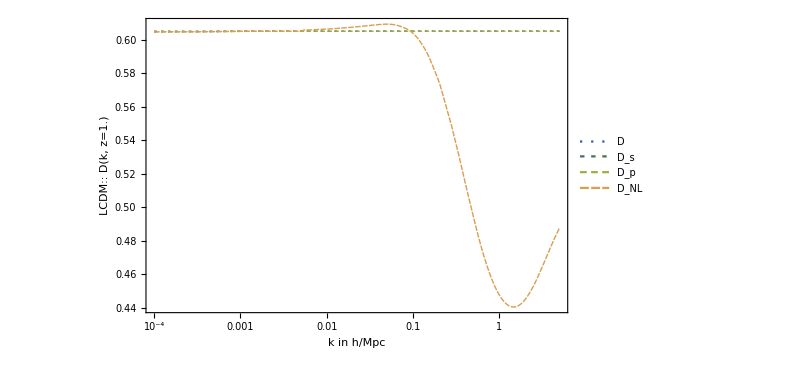

```mathematica
modelnum=0;
modelname=modelnum/.modelsnamerule;
kvall=0.5;
zvall=1.0;
LogLinearPlot[{growthCAMBInterp[modelnum][zvall, kk],s8growthInterp[modelnum][zvall],growthRatioPksLinTabInterp[modelnum][zvall,kk], growthRatioPksNonLinTabInterp[modelnum][zvall,kk]}, {kk,0.0001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"D","D_s","D_p", "D_NL"}], Scaled[{0.15,0.3}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style[modelname<>":: "<>"D(k, z="<>ToString[zvall]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

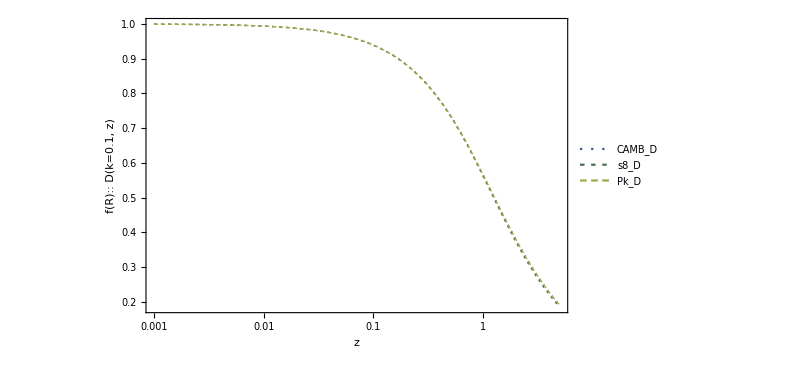

```mathematica
modelnum=3;
modelname=modelnum/.modelsnamerule;
kvall=0.1;
LogLinearPlot[{growthCAMBInterp[modelnum][zz, kvall],s8growthInterp[modelnum][zz],growthRatioPksLinTabInterp[modelnum][zz,kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"CAMB_D","s8_D","Pk_D"}], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style[modelname<>":: "<>"D(k="<>ToString[kvall]<>", z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

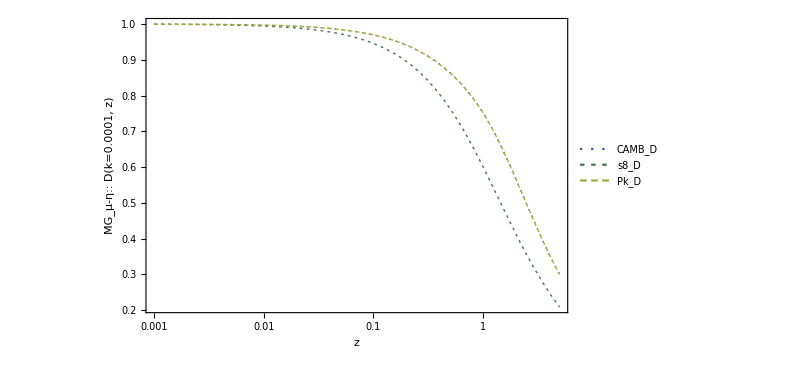

```mathematica
modelnum=4;
modelname=modelnum/.modelsnamerule;
kvall=0.0001;  (*Differences only at very large scales*)
LogLinearPlot[{growthCAMBInterp[modelnum][zz, kvall],s8growthInterp[modelnum][zz],growthRatioPksLinTabInterp[modelnum][zz,kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"CAMB_D","s8_D","Pk_D"}], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style[modelname<>":: "<>"D(k="<>ToString[kvall]<>", z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

0.001

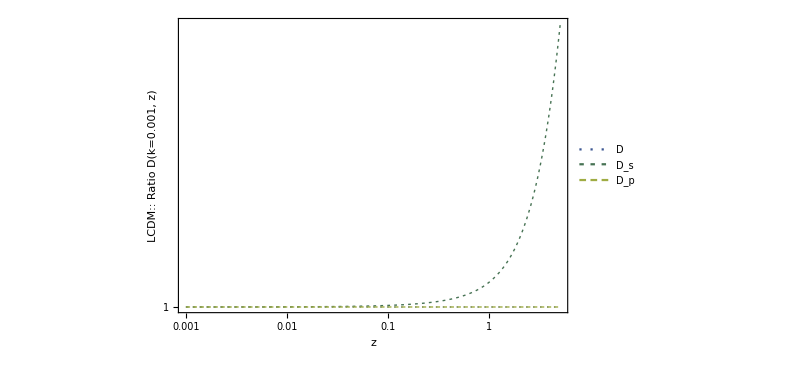

```mathematica
kvall=0.001
modelnum=0;
modelname=modelnum/.modelsnamerule;
LogLogPlot[{growthCAMBInterp[modelnum][zz, kvall]/growthCAMBInterp[modelnum][zz, kvall],s8growthInterp[modelnum][zz]/growthCAMBInterp[modelnum][zz, kvall],growthRatioPksLinTabInterp[modelnum][zz,kvall]/growthCAMBInterp[modelnum][zz, kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"D","D_s","D_p"}], Scaled[{0.25,0.5}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,14], Style[modelname<>":: "<>"Ratio D(k="<>ToString[kvall]<>", z)", Bold, 14]} , ImageSize->600, FrameTicksStyle->Directive[Black,14],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

0.1

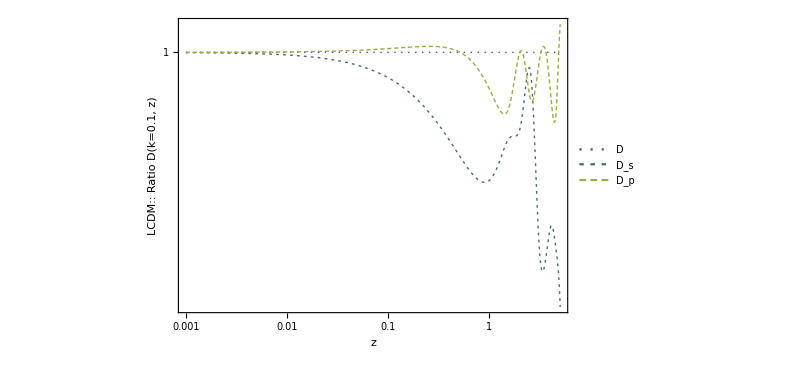

```mathematica
kvall=0.1
modelnum=0;
modelname=modelnum/.modelsnamerule;
LogLogPlot[{growthCAMBInterp[modelnum][zz, kvall]/growthCAMBInterp[modelnum][zz, kvall],s8growthInterp[modelnum][zz]/growthCAMBInterp[modelnum][zz, kvall],growthRatioPksLinTabInterp[modelnum][zz,kvall]/growthCAMBInterp[modelnum][zz, kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"D","D_s","D_p"}], Scaled[{0.25,0.5}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,14], Style[modelname<>":: "<>"Ratio D(k="<>ToString[kvall]<>", z)", Bold, 14]} , ImageSize->600, FrameTicksStyle->Directive[Black,14],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

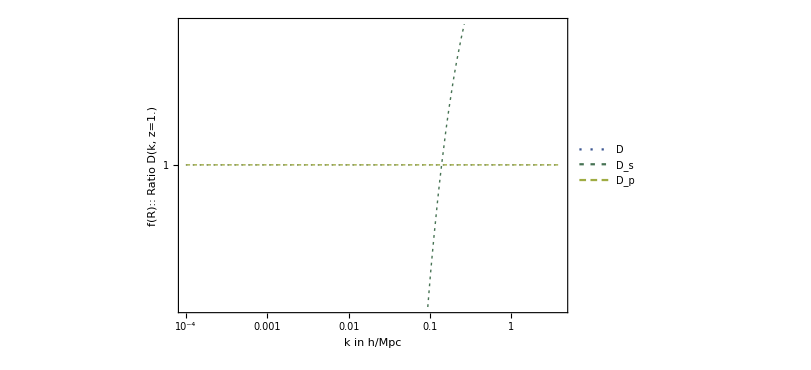

```mathematica
kvall=0.001;
zvall=1.0;
modelnum=3;
modelname=modelnum/.modelsnamerule;
LogLogPlot[{growthCAMBInterp[modelnum][zvall, kk]/growthCAMBInterp[modelnum][zvall, kk],s8growthInterp[modelnum][zvall]/growthCAMBInterp[modelnum][zvall, kk],growthRatioPksLinTabInterp[modelnum][zvall,kk]/growthCAMBInterp[modelnum][zvall, kk]}, {kk,0.0001,4.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"D","D_s","D_p"}], Scaled[{0.8,0.5}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,14], Style[modelname<>":: "<>"Ratio D(k, z="<>ToString[zvall]<>")", Bold, 14]} , ImageSize->600, FrameTicksStyle->Directive[Black,14],
PlotRange->{0.99,1.01}(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

## Plot LCDM different options for Growth Rate f(k,z)

```mathematica
Names["*Interp"]
```

{fgRatioPksLinInterp,fgRatioPksNonLinInterp,fgrowthrateCAMBInterp,growthCAMBInterp,growthRatioPksLinTabInterp,growthRatioPksNonLinTabInterp,pkLinInterp,pkNonLinInterp,s8fgrowthrateInterp,s8growthInterp}

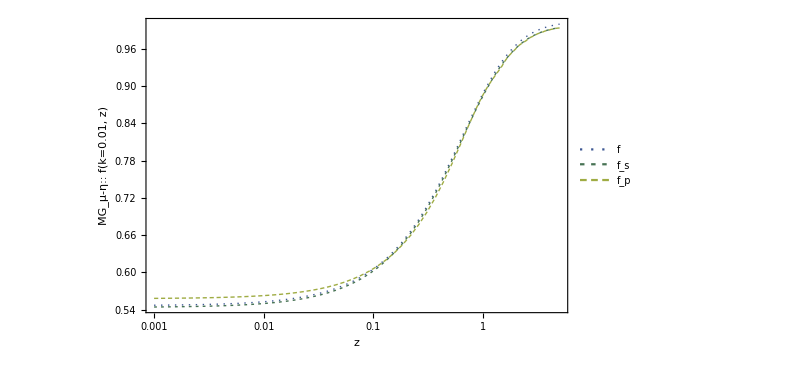

```mathematica
modelnum=4;
modelname=modelnum/.modelsnamerule;
kvall=0.01;
LogLinearPlot[{fgrowthrateCAMBInterp[modelnum][zz, kvall],s8fgrowthrateInterp[modelnum][zz],fgRatioPksLinInterp[modelnum][zz,kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"f","f_s","f_p"}], Scaled[{0.15,0.7}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style[modelname<>":: "<>"f(k="<>ToString[kvall]<>", z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

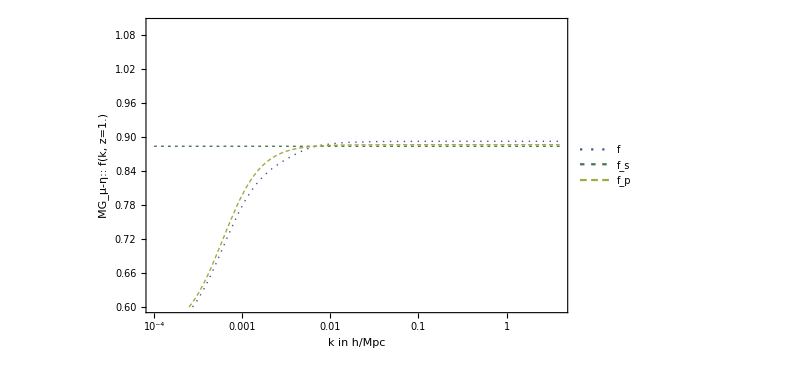

```mathematica
modelnum=4;
modelname=modelnum/.modelsnamerule;
kvall=0.001;
zvall=1.0;
LogLinearPlot[{fgrowthrateCAMBInterp[modelnum][zvall, kkk],s8fgrowthrateInterp[modelnum][zvall],fgRatioPksLinInterp[modelnum][zvall,kkk]}, (*{zz,0.001,5.0}*){kkk,0.0001,4},
PlotLegends->Placed[LineLegend[{"f","f_s","f_p"}], Scaled[{0.85,0.3}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style[modelname<>":: "<>"f(k, z="<>ToString[zvall]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->{0.6,1.1}(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

0.1

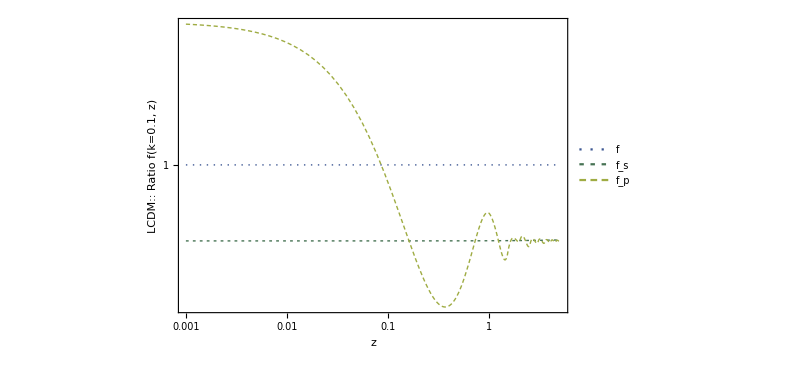

```mathematica
kvall=0.1
modelnum=0;
modelname=modelnum/.modelsnamerule;
LogLogPlot[{fgrowthrateCAMBInterp[modelnum][zz, kvall]/fgrowthrateCAMBInterp[modelnum][zz, kvall],s8fgrowthrateInterp[modelnum][zz]/fgrowthrateCAMBInterp[modelnum][zz, kvall],fgRatioPksLinInterp[modelnum][zz,kvall]/fgrowthrateCAMBInterp[modelnum][zz, kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"f","f_s","f_p"}], Scaled[{0.85,0.75}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style[modelname<>":: "<>"Ratio f(k="<>ToString[kvall]<>", z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

0.1

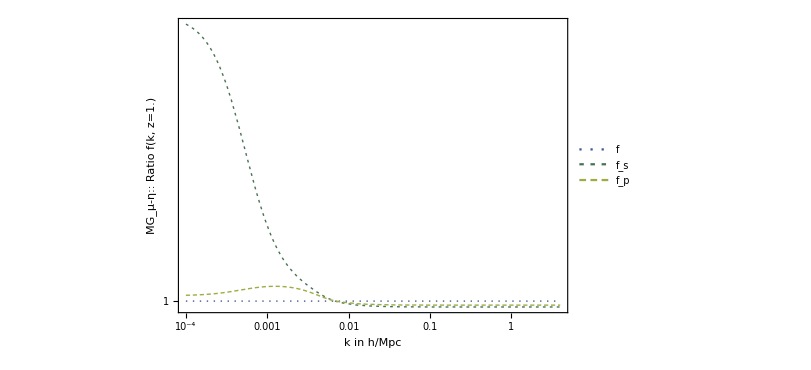

```mathematica
kvall=0.1
modelnum=4;
zvall=1.0;
modelname=modelnum/.modelsnamerule;
LogLogPlot[{fgrowthrateCAMBInterp[modelnum][zvall, kkk]/fgrowthrateCAMBInterp[modelnum][zvall, kkk],s8fgrowthrateInterp[modelnum][zvall]/fgrowthrateCAMBInterp[modelnum][zvall, kkk],fgRatioPksLinInterp[modelnum][zvall,kkk]/fgrowthrateCAMBInterp[modelnum][zvall, kkk]}, (*{zz,0.001,5.0}*){kkk,0.0001,4},
PlotLegends->Placed[LineLegend[{"f","f_s","f_p"}], Scaled[{0.85,0.75}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style[modelname<>":: "<>"Ratio f(k, z="<>ToString[zvall]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```